```mathematica
m = 5;
n = 20;
```

```mathematica
A = RandomReal[{-10, 10}, {n, n}];
sparsity = Round[0.6RandomReal[{-1, 1}, {n, n}]];
sparsity = Transpose[sparsity].sparsity;
A = Transpose[A].A * sparsity;
f = RandomReal[{-1, 1}, n];
B = RandomReal[{-1, 1}, {n, m}] * Round[0.75RandomReal[{-1, 1}, {n, m}]];
g = RandomReal[{-1, 1}, m];
```

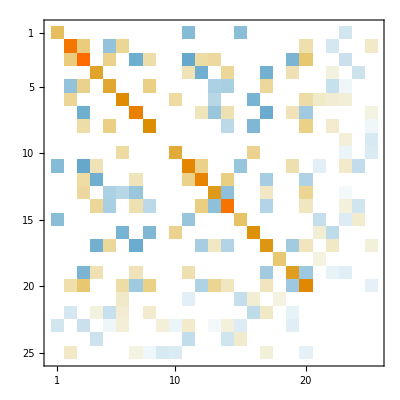

```mathematica
H = ArrayFlatten[({{A, B}, {Transpose[B], 0}})];
y = Join[f, g];
{x, λ} = TakeList[LinearSolve[H, y], {n, m}];
MatrixPlot[H]
```

```mathematica
{rrefBT, ghat} = Transpose /@ TakeList[Transpose[RowReduce[ArrayFlatten[({{Transpose[B], Transpose[{g}]}})]]],{n, 1}] ;
ghat = Flatten[ghat];
```

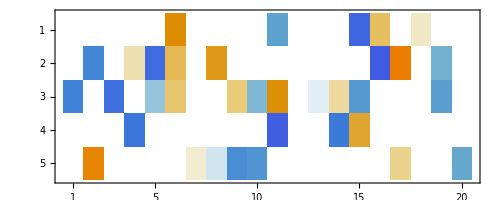

```mathematica
MatrixPlot[Transpose[B]]
```

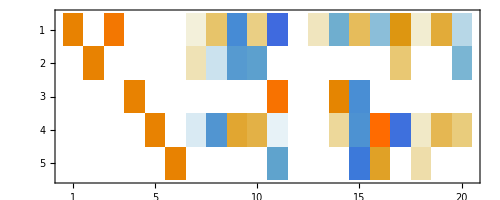

```mathematica
MatrixPlot[rrefBT]
```

```mathematica
eliminatedIds={};
Do[
If[Norm[rrefBT[[All, i]]-IdentityMatrix[m][[All, Length[eliminatedIds]+1]]] < 10^-8,
AppendTo[eliminatedIds, i];
];
If[Length[eliminatedIds]==m, Break[]],
{i, 1, n}
]
keptIds = Complement[Table[i, {i, 1, n}], eliminatedIds];
```

```mathematica
Z = ConstantArray[0, {n, Length[keptIds]}];
Z[[keptIds]] = IdentityMatrix[Length[keptIds]];
Z[[eliminatedIds]] = -rrefBT[[All, keptIds]];
```

```mathematica
xhat = LinearSolve[Transpose[Z].A.Z,Transpose[Z].f - Transpose[Z].A[[All, eliminatedIds]].ghat];
x2 = Z.xhat;
x2[[eliminatedIds]] += Flatten[ghat];
x2
```

{0.169145,-0.0831377,0.0472605,-0.156378,-0.0352696,0.144491,0.00236438,0.0504511,0.799728,0.126948,-0.311828,0.0225804,-0.00447274,-0.100473,-0.0972512,0.044042,0.0118211,0.095703,0.0779117,0.0147558}

```mathematica
x
```

{0.169145,-0.0831377,0.0472605,-0.156378,-0.0352696,0.144491,0.00236438,0.0504511,0.799728,0.126948,-0.311828,0.0225804,-0.00447274,-0.100473,-0.0972512,0.044042,0.0118211,0.095703,0.0779117,0.0147558}